# Lens geometry cell

## Setup

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory@NotebookDirectory[]
Get["MyPackage.wl"]
```

C:\Universita\MAGISTRALE\MasterThesis\Mathematica

```mathematica
arrowcycle[]:= Line[x_]:>{Arrowheads[{0,0,0.05,0}],Arrow[x]}
```

```mathematica
opts={GridLines->Automatic,GridLinesStyle->LightGray,LabelStyle->{Black,Bold,FontFamily->"Times New Roman",FontSize->12},AxesStyle->{FontFamily->"Times New Roman"},Frame->True};
```

```mathematica
alldata=Import["lenscell_data.m"]
```

<|cellVal→{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,w0→1/10,tp0→1/40000,tf0→1/100000,ϵ1max→0.05},tankVal→{d→5,Pt→50000,Vtank→1,Vftot→1,f→0.1},gasVal→{patm→101325,Tstd→288.15,γair→1.4,ρstdair→1.225,cv→717.2,cp→1.0042}|>

```mathematica
celldata=alldata["cellVal"]
```

{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,w0→1/10,tp0→1/40000,tf0→1/100000,ϵ1max→0.05}

## Model

```mathematica
data0test={h0-> 0.5 10^-3,l0->0.5 10^-2};
```

-Graphics-

```mathematica
solvegeom[h0_,l0_,pts_:100,interpdegree_:0]:=Module[{θ0,R0,areaarc0,area,hvec,lcvec,Rtmp,Rvec,Δhvec,θvec,R,lc,α0,θ},
If[NumericQ[h0]&&NumericQ[l0],
θ0=α0/.FindRoot[((h0-l0/α0(1-Cos[α0/2])))==0,{α0,ArcCos[(2 h0)/l0]}];
R0=l0/θ0;
areaarc0=1/2 R0^2(θ0-Sin@θ0);
area=R lc(1-Cos[(l0-lc)/(2 R)])+R^2/2((l0-lc)/R-Sin[(l0-lc)/R]);
lcvec=LinSpace[0,l0-l0/3,pts];
Rtmp={R0};
Rvec=Flatten@Table[Rtmp=R/.FindRoot[(area==areaarc0)/.lc->lcvec[[i]],{R,Rtmp}],{i,1,Length@lcvec}];
θvec=(l0-lc)/R/.{lc->lcvec,R->Rvec};
hvec=R(1-Cos[θ/2])/.{R->Rvec,θ->θvec};
Δhvec=hvec[[1]]-hvec;
If[interpdegree!=0,
Module[{lcint,Rint,θint},
lcint=Interpolation[Transpose[{Δhvec,lcvec}],InterpolationOrder->3];
Rint=Interpolation[Transpose[{Δhvec,Rvec}],InterpolationOrder->3];
θint=Interpolation[Transpose[{Δhvec,θvec}],InterpolationOrder->3];
{lcint,Rint,θint}]
,
{hvec,lcvec,Rvec,θvec}]
]]
```

```mathematica
Clear[DrawHalfCellDown,DrawHalfCellUp,DrawCell]
DrawHalfCellUp[hlcRθ_,hlcRθ0_List:{},xyshift_List:{0,0},tf0_:(tf0/.celldata)]:=
Module[{CarcAB,CarcCD,θAB,θCD,B,C,CarcAB0,CarcCD0,θAB0,θCD0,lc,R,h,θ,h0,lc0,R0,θ0,halfcell,xyshift0,halfcell0},
CarcAB={-lc/2,-(R-h)}+xyshift;θAB=π/2+{0,θ/2};B={-lc/2,h}+xyshift;
CarcCD={lc/2,-(R-h)}+xyshift;θCD=π/2+{0,-θ/2};C={lc/2,h}+xyshift;
halfcell={Circle[CarcAB,R,θAB],Line[{B,C}],Circle[CarcCD,R,θCD]};
If[Length@hlcRθ0==4,{h0,lc0,R0,θ0}=hlcRθ0;xyshift0={xyshift[[1]],xyshift[[2]]/(2hlcRθ[[1]]+tf0)(2hlcRθ0[[1]]+tf0)};
CarcAB0={-lc0/2,-(R0-h0)}+xyshift0;θAB0=π/2+{0,θ0/2};
CarcCD0={lc0/2,-(R0-h0)}+xyshift0;θCD0=π/2+{0,-θ0/2};
halfcell0={Circle[CarcAB0,R0,θAB0],Circle[CarcCD0,R0,θCD0]};
,halfcell0={}];
Graphics[{Darker@Red,Dashed,halfcell0,Thick,Dashing@None,halfcell/.{h->hlcRθ[[1]],lc->hlcRθ[[2]],R->hlcRθ[[3]],θ->hlcRθ[[4]]}}]
]
DrawHalfCellDown[hlcRθ_,hlcRθ0_List:{},xyshift_List:{0,0},tf0_:(tf0/.celldata)]:=
Module[{CarcAB,CarcCD,θAB,θCD,B,C,CarcAB0,CarcCD0,θAB0,θCD0,lc,R,h,θ,h0,lc0,R0,θ0,halfcell,xyshift0,halfcell0},
CarcAB={-lc/2,(R-h)}+xyshift;θAB=3π/2+{0,-θ/2};B={-lc/2,-h}+xyshift;
CarcCD={lc/2,(R-h)}+xyshift;θCD=3π/2+{0,θ/2};C={lc/2,-h}+xyshift;
halfcell={Circle[CarcAB,R,θAB],Line[{B,C}],Circle[CarcCD,R,θCD]};
If[Length@hlcRθ0==4,{h0,lc0,R0,θ0}=hlcRθ0;xyshift0={xyshift[[1]],xyshift[[2]]/(2hlcRθ[[1]]+tf0)(2hlcRθ0[[1]]+tf0)};
CarcAB0={-lc0/2,(R0-h0)}+xyshift0;θAB0=3π/2+{0,-θ0/2};
CarcCD0={lc0/2,(R0-h0)}+xyshift0;θCD0=3π/2+{0,θ0/2};
halfcell0={Circle[CarcAB0,R0,θAB0],Circle[CarcCD0,R0,θCD0]};
,halfcell0={}];
Graphics[{Darker@Red,Dashed,halfcell0,Thick,Dashing@None,halfcell/.{h->hlcRθ[[1]],lc->hlcRθ[[2]],R->hlcRθ[[3]],θ->hlcRθ[[4]]}}]
]
DrawCell[hlcRθ_,hlcRθ0_List:{},xyshift_List:{0,0},tf0_:(tf0/. celldata)]:=
Show[
DrawHalfCellUp[hlcRθ,hlcRθ0,xyshift,tf0],
DrawHalfCellDown[hlcRθ,hlcRθ0,xyshift,tf0]
]
```

### Test geometries

```mathematica
h0range=h0{0.5,1,1.5}/.data0test;l0range=l0{0.5,1,1.5}/.data0test;
h0strings=Table[StringJoin["h_0 = ",ScientString[h0range[[i]]//N,3]," [m]"],{i,1,Length@h0range}]
l0strings=Table[StringJoin["l_0 = ",ScientString[l0range[[i]]//N,3]," [m]"],{i,1,Length@l0range}]
```

{h_0 = 2.5×10^-4 [m],h_0 = 5.×10^-4 [m],h_0 = 7.5×10^-4 [m]}

{l_0 = 2.5×10^-3 [m],l_0 = 5.×10^-3 [m],l_0 = 7.5×10^-3 [m]}

```mathematica
geomhl=Table[solvegeom[h0range[[i]],l0range[[j]],100],{i,1,Length@h0range},{j,1,Length@l0range}];(*geomhl[[i,j]] -> h0range[[i]],l0range[[j]]*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Manipulate[Column[
Table[Row[
Flatten@Table[{Block[{hlcRθ=geomhl[[i,j,;;,idx]],hlcRθ0=If[undef==1,geomhl[[i,j,;;,1]],{}],tf0=tf0/.celldata},
Show[DrawCell[hlcRθ,hlcRθ0],PlotLabel->Row[{h0strings[[i]],Spacer@10,l0strings[[j]]}],
Axes->True,ImageSize->350,PlotRange->{0.95l0range[[j]]{-1,1},1.2h0range[[i]]{-1,1}},AspectRatio->(5 h0range[[i]])/l0range[[3]],Frame->True,Evaluate@opts]],Spacer@10},{i,1,Length@h0range}]],{j,1,Length@l0range}]
],{idx,1,100,1},{{undef,1,"Undeformed"},{0,1}}]
```

## Cell analysis

### Double cell unit

```mathematica
data0={h0->h0range[[2]],l0->l0range[[2]]};
cellidx=2;
```

```mathematica
cellvec=solvegeom[h0/.data0,l0/.data0,1000];
hvec=cellvec[[1]];lcvec=cellvec[[2]];Rvec=cellvec[[3]];θvec=cellvec[[4]];
```

```mathematica
cell=solvegeom[h0/.data0,l0/.data0,1000,1]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Manipulate[Block[{hlcRθ=cellvec[[;;,idx]],hlcRθ0=If[undef==1,cellvec[[;;,1]],{}],tf0=10tf0/.celldata},
Show[
Table[DrawCell[hlcRθ,hlcRθ0,(i-1){0,2hlcRθ[[1]]+tf0},tf0],{i,1,2}],
PlotLabel->StringJoin["Δh = ",ScientString[hvec[[1]]-hlcRθ[[1]],3], " [m]"],
Evaluate@opts,PlotRange->{0.6(l0/.data0){-1,1},(h0/.data0){-1.1,4}}
]]
,{idx,1,Length@cellvec[[1]],1},{{undef,1,"Undeformed"},{0,1}}]
```

```mathematica
lc=cell[[1]];
dlc=D[lc[Δh],Δh][[0]]
dhdom=lc["Domain"]//Flatten;dhdom//ScientificForm
```

InterpolatingFunction[…]

{0.,1.22022×10^-4}

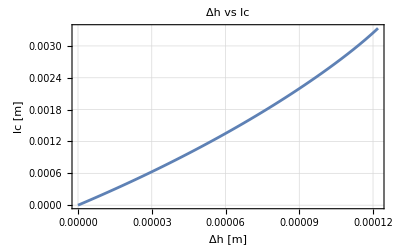
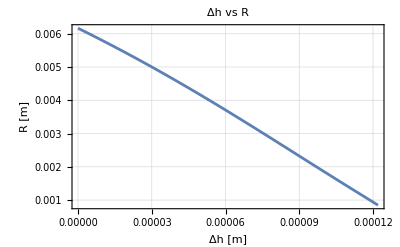
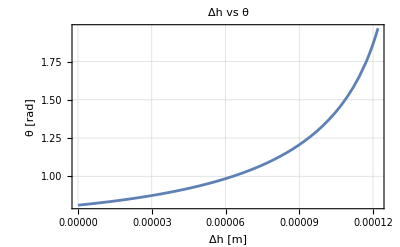

```mathematica
Row[{
Plot[lc[Δh],{Δh,dhdom[[1]],dhdom[[2]]},ImageSize->400,Evaluate@opts,PlotLabel->"Δh vs lc",FrameLabel->{"Δh [m]","lc [m]"}],Spacer@10,
Plot[cell[[2]][Δh],{Δh,dhdom[[1]],dhdom[[2]]},ImageSize->400,Evaluate@opts,PlotLabel->"Δh vs R",FrameLabel->{"Δh [m]","R [m]"}],Spacer@10,
Plot[cell[[3]][Δh],{Δh,dhdom[[1]],dhdom[[2]]},ImageSize->400,Evaluate@opts,PlotLabel->"Δh vs θ",FrameLabel->{"Δh [m]","θ [rad]"}]
}]
```

```mathematica
CC[Δh_]:=(((ϵp w0 lcc[Δh])/(2 tp0))^-1+((ϵf w0 lcc[Δh])/tf0)^-1)^-1//Simplify
```

```mathematica
CC[dh]
```

(w0 ϵf ϵp lcc[dh])/(2 tp0 ϵf+tf0 ϵp)

```mathematica
D[CC[dh],dh]
```

(w0 ϵf ϵp lcc'[dh])/(2 tp0 ϵf+tf0 ϵp)

```mathematica
Vrange=Range[0,6000,2000];
Vstrings=Table[StringJoin["V = ",ScientString[Vrange[[i]],3]," [V]"],{i,1,Length@Vrange}];
```

```mathematica
F[Δh_,V_,lcint_]:=(V^2/2 D[CC[dh],dh])/.D[lcc[dh],dh]->(D[lcint[dh],dh][[0]][Δh])
```

```mathematica
Fcell[Δh_,V_]:=F[Δh,V,lc]/.celldata
```

```mathematica
ΔhvecUel=Range[dhdom[[1]],dhdom[[2]],10^-7];
```

```mathematica
Uel=ParallelTable[NIntegrate[Fcell[Δh,Last@Vrange],{Δh,dhdom[[1]],Δhmax},Method->{"Trapezoidal","SymbolicProcessing"->0}],{Δhmax,dhdom[[1]],dhdom[[2]],10^-7}];
```

```mathematica
l=l0/.data0;A=1/2 R^2(θ-Sin@θ)/.{R->Rvec[[1]],θ->θvec[[1]]};
Vol=A w0+tp0 w0 l/.celldata
```

1.75998×10^-7

```mathematica
uel=Uel/Vol;
```

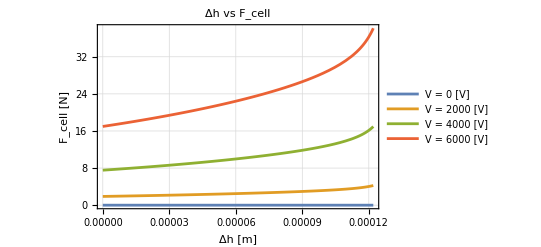

```mathematica
Plot[Evaluate@Fcell[Δh,Vrange],{Δh,dhdom[[1]],dhdom[[2]]},Evaluate@opts,FrameLabel->{"Δh [m]","F_cell [N]"},PlotLabel->"Δh vs F_cell",PlotLegends->Vstrings]
```

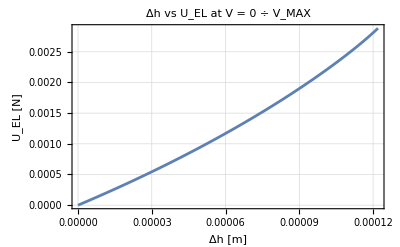
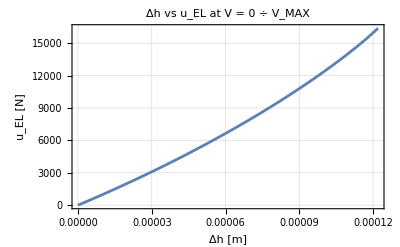

```mathematica
Row[{
ListPlot[Transpose[{ΔhvecUel,Uel}],Joined->True,Evaluate@opts,FrameLabel->{"Δh [m]","U_EL [N]"},PlotLabel->"Δh vs U_EL at V = 0 ÷ V_MAX"],
ListPlot[Transpose[{ΔhvecUel,Uel/Vol}],Joined->True,Evaluate@opts,FrameLabel->{"Δh [m]","u_EL [N]"},PlotLabel->"Δh vs u_EL at V = 0 ÷ V_MAX"]
}]
```

### Varying h_0 and l_0

```mathematica
smallergeom={solvegeom[h0range[[1]],l0range[[1]],1000,1],h0->h0range[[1]],l0->l0range[[1]]};
biggergeom={solvegeom[h0range[[3]],l0range[[3]],1000,1],h0->h0range[[3]],l0->l0range[[3]]};
```

```mathematica
lcsmaller=smallergeom[[1,1]];
dhsmaller=lcsmaller["Domain"]//Flatten
lcbigger=biggergeom[[1,1]];
dhbigger=lcbigger["Domain"]//Flatten
```

{0.,0.000061011}

{0.,0.000183033}

```mathematica
Fsmaller[Δh_,V_]:=F[Δh,V,lcsmaller]/.celldata
Fbigger[Δh_,V_]:=F[Δh,V,lcbigger]/.celldata
```

```mathematica
forces={Fsmaller[Δh,Last@Vrange],Fcell[Δh,Last@Vrange],Fbigger[Δh,Last@Vrange]};
```

```mathematica
dhdoms={dhsmaller,dhdom,dhbigger};
dhdomsnorm=dhdoms/l0range;
```

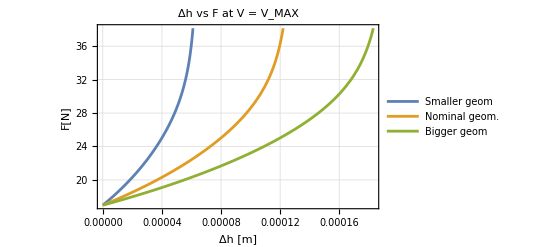

```mathematica
Show[
Plot[Fsmaller[Δh,Last@Vrange],{Δh,dhsmaller[[1]],dhsmaller[[2]]},PlotStyle->DefColors[1],PlotLegends->{"Smaller geom"}],
Plot[Fcell[Δh,Last@Vrange],{Δh,dhdom[[1]],dhdom[[2]]},PlotStyle->DefColors[2],PlotLegends->{"Nominal geom."}],
Plot[Fbigger[Δh,Last@Vrange],{Δh,dhbigger[[1]],dhbigger[[2]]},PlotStyle->DefColors[3],PlotLegends->{"Bigger geom"}],
PlotRange->All,Evaluate@opts,FrameLabel->{"Δh [m]","F[N]"},PlotLabel->"Δh vs F at V = V_MAX"
]
```

```mathematica
lgeoms=l0range;
Ageoms=1/2 R^2(θ-Sin@θ)/.{R->{smallergeom[[1,2]][0],Rvec[[1]],biggergeom[[1,2]][0]},θ->{smallergeom[[1,3]][0],θvec[[1]],biggergeom[[1,3]][0]}};
Volgeoms=Ageoms w0+tp0 w0 lgeoms/.celldata
```

{4.71246×10^-8,1.75998×10^-7,3.86621×10^-7}

```mathematica
Uelgeoms=Table[ParallelTable[NIntegrate[forces[[i]],{Δh,dhdoms[[i,1]],Δhmax},Method->{"Trapezoidal","SymbolicProcessing"->0}],{Δhmax,dhdoms[[i,1]],dhdoms[[i,2]],10^-6}],{i,1,Length@forces}];
```

```mathematica
Δhgeoms=Table[Range[dhdoms[[i,1]],dhdoms[[i,2]],10^-6],{i,1,Length@forces}];
```

```mathematica
uelgeoms=Uelgeoms/Volgeoms;
```

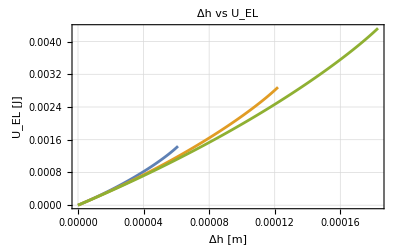
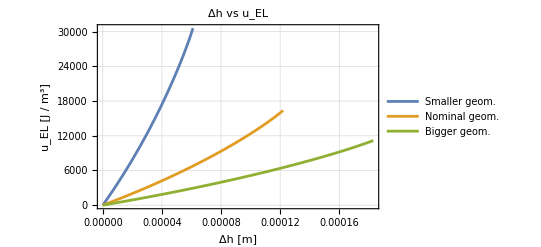

```mathematica
Row[{
ListPlot[Table[Transpose[{Δhgeoms[[i]],Uelgeoms[[i]]}],{i,1,Length@forces}],Joined->True,Evaluate@opts,FrameLabel->{"Δh [m]","U_EL [J]"},PlotLabel->"Δh vs U_EL"],Spacer@10,
ListPlot[Table[Transpose[{Δhgeoms[[i]],uelgeoms[[i]]}],{i,1,Length@forces}],Joined->True,Evaluate@opts,FrameLabel->{"Δh [m]","u_EL [J / m^3]"},PlotLabel->"Δh vs u_EL",PlotLegends->{"Smaller geom.","Nominal geom.","Bigger geom."}]}]
```

### Q-V plot

C = Q / V

```mathematica
Δhvec=hvec[[1]]-hvec;
```

```mathematica
Ccell[Δh_]:=CC[Δh]/.celldata/.lcc[Δh]->lc[Δh]
```

```mathematica
lc[dhdom[[1]]]
```

-4.23516×10^-22

```mathematica
Cvec=Clip[Ccell[Δhvec],{0,Infinity}];
```

```mathematica
{Cmin=Cvec[[1]],Cmax=Last@Cvec}
```

{0.,1.60243×10^-10}

```mathematica
Vmaxdef=LinSpace[0,Last@Vrange,Length@Cvec];
```

```mathematica
Qmaxdef=Cmax Vmaxdef;
```

```mathematica
Vmindef=LinSpace[0,Last@Vrange,Length@Cvec];
```

```mathematica
Qmindef=Cmin Vmindef;
```

```mathematica
QVmax=LinSpace[0,Last@Qmaxdef,Length@Cvec];
```

```mathematica
Vmaxvec=ConstantArray[Last@Vrange,Length@Cvec];
```

```mathematica
QVpl[style_]:=ListPlot[{
Transpose[{Qmindef,Vmindef}],Transpose[{Qmaxdef,Vmaxdef}],Transpose[{QVmax,Vmaxvec}]},PlotStyle->style,
Joined->True,FrameLabel->{"Q [A]","V [V]"},PlotLabel->"Q vs V",Evaluate@opts,PlotLegends->{"Min. def.","Max. def.","V_MAX"}]
```

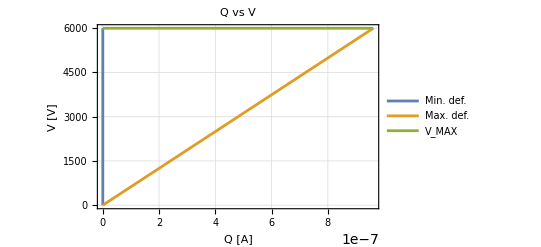

```mathematica
QVpl[Automatic]
```

```mathematica
UelQV=CumTrapz[QVmax,Vmaxvec]-CumTrapz[Qmaxdef,Vmaxdef];
```

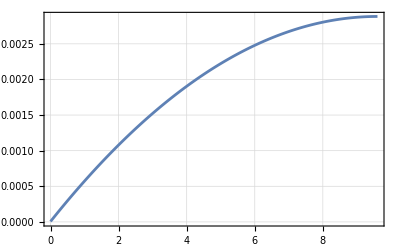

```mathematica
ListPlot[Transpose[{QVmax[[1;;Length@UelQV]],UelQV}],Joined->True,PlotRange->All,Evaluate@opts]
```

#### Q-V plots in working condition

```mathematica
FVmax=Fcell[Δh,Last@Vrange]
```

0.86531 InterpolatingFunction[…][Δh]

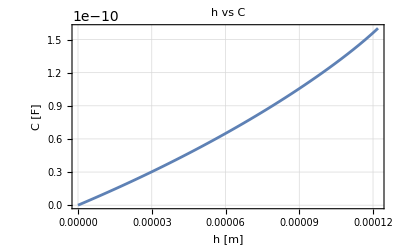

```mathematica
Plot[Ccell[Δh],{Δh,dhdom[[1]],dhdom[[2]]},Evaluate@opts,FrameLabel->{"h [m]","C [F]"},PlotLabel->"h vs C"]
```

```mathematica
fixedhpath[n_,Δhleft_,Δhright_,FintV0_,FintVmax_,Vrange_]:=Module[{hA,hB,hC,hD,hrangeAB,hrangeBC,hrangeCD,hrangeDA,VAB,VBC,VCD,VDA,CAB,CBC,CCD,CDA,QAB,QBC,QCD,QDA},
hA=Δhright;
hB=Δhleft;
hC=hB;
hD=hA;
hrangeAB=LinSpace[hA,hB,n];hrangeBC=ConstantArray[hB,n];hrangeCD=LinSpace[hC,hD,n];hrangeDA=ConstantArray[hA,n];
VAB=ConstantArray[Vrange[[1]],n];VBC=LinSpace[Vrange[[1]],Last@Vrange,n];VCD=ConstantArray[Last@Vrange,n];VDA=LinSpace[Last@Vrange,Vrange[[1]],n];
CAB=Ccell/. h->hrangeAB;CBC=Ch/.h->hrangeBC;CCD=Ch/.h->hrangeCD;CDA=Ch/.h->hrangeDA;
QAB=CAB VAB;QBC=CBC VBC;QCD=CCD VCD;QDA=CDA VDA;
{{{hA,FintV0[hA]},{hB,FintV0[hB]},{hC,FintVmax[hC]},{hD,FintVmax[hD]}},{hrangeAB,hrangeBC,hrangeCD,hrangeDA},{VAB,VBC,VCD,VDA},{CAB,CBC,CCD,CDA},{QAB,QBC,QCD,QDA}}]
```

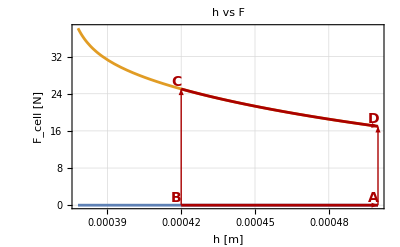
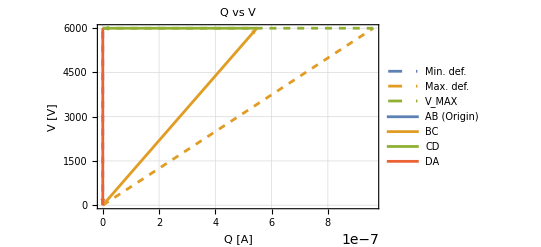

```mathematica
Module[{hleft=0.00042,hright=h0/.data0,xtol=0.000002,ytol=1.5},
{ptsh,hrangesh,Vrangesh,Crangesh,Qrangesh}=fixedhpath[100,hleft,hright,FintVmin,FintVmax,Vrange];
Row[{
Show[
Plot[{FintVmin[h],FintVmax[h]},{h,hdom[[1]],hdom[[2]]},Evaluate@opts,FrameLabel->{"h [m]","F_cell [N]"},PlotLabel->"h vs F"],
Plot[{FintVmin[h]},{h,hleft,hright},PlotStyle->Darker@Red] /.MidArrow[-1],
Plot[{FintVmax[h]},{h,hleft,hright},PlotStyle->Darker@Red] /.MidArrow[1],
Graphics[{Thick,Darker@Red,
Line[{{hleft,FintVmin@hleft},{hleft,FintVmax@hleft}}]/.MidArrow[1],
Line[{{hright,FintVmin@hright},{hright,FintVmax@hright}}]/.MidArrow[-1],
MapThread[Text[Style[#1,{Bold,14,FontFamily->"Consolas"}],#2+{-xtol,ytol}]&,{{"A","B","D","C"},Flatten[Table[{j,i[j]},{i,{FintVmin,FintVmax}},{j,{hright,hleft}}],1]}]}]
],
Show[
QVpl[Dashed],
ListPlot[Table[Transpose[{Qrangesh[[i]],Vrangesh[[i]]}],{i,1,Length@Qrangesh}],Joined->True,PlotLegends->{"AB (Origin)","BC","CD","DA"},Evaluate@opts]/.MidArrow[1]]}]

]
```

### Stack

```mathematica
Manipulate[Block[{lim=l0/.data0,tf0=tf0/.celldata},
Show[Table[DrawCell[cell,idx,{(-Floor[Nc/2]+j-1) l0/.data0,{2(i-1)(hvec[[idx]]+tf0),tf0}},dash],{j,1,Nc},{i,1,Ns}],
PlotLabel->Row[{h0strings[[cellidx]]," ",l0strings[[cellidx]]}],Evaluate@opts,ImageSize->1100,LabelStyle->{Black,Bold},Axes->True,PlotRange-> 4(l0/.data0){{-1,1},{-0.1,0.3}}]]
,{{dash,1,"Undeformed"},{0,1}},
Row[{Control[{{idx,1,"h"},1,Length@cell[[1]],1}],Dynamic@hvec[[idx]],Spacer@10,Control[{Nc,1,7,1}],Spacer@10,Control[{{Ns,5},1,5,1}]}]]
```

ReplaceAll::reps: {data0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification hvec⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {data0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification hvec⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression cellidx cannot be used as a part specification.

Show::gcomb: Could not combine the graphics objects in Show[{{DrawCell[cell,1,{0/.data0,{0,1/100000}},1],DrawCell[cell,1,{0/.data0,{2 Plus[«2»],1/100000}},1],DrawCell[cell,1,{0/.data0,{4 Plus[«2»],1/100000}},1],DrawCell[cell,1,{0/.data0,{6 Plus[«2»],1/100000}},1],DrawCell[cell,1,{0/.data0,{8 Plus[«2»],1/100000}},1]}},PlotLabel→h0strings,{GridLines→Automatic,GridLinesStyle→color,LabelStyle→{color,Bold,FontFamily→Times New Roman,FontSize→12},AxesStyle→{FontFamily→Times New Roman},Frame→True},ImageSize→1100,LabelStyle→{color,Bold},Axes→True,PlotRange→{{-4 (l0/.data0),4 (l0/.data0)},{-0.4 (l0/.data0),1.2 (l0/.data0)}}].

ReplaceAll::reps: {data0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {celldata} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {data0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification hvec⟦1⟧ is longer than depth of object.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Part::partd: Part specification hvec⟦1⟧ is longer than depth of object.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

Part::partd: Part specification hvec⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 64 exceeded.

General::stop: Further output of $RecursionLimit::reclim will be suppressed during this calculation.

Part::pkspec1: The expression cellidx cannot be used as a part specification.

Show::gcomb: Could not combine the graphics objects in Show[{{Hold[DrawCell[cell,FE`idx$$50,{Times[«2»]/.data0,{Times[«2»],tf0}},FE`dash$$50]],Hold[DrawCell[cell,FE`idx$$50,{Times[«2»]/.data0,{Times[«2»],tf0}},FE`dash$$50]],Hold[DrawCell[cell,FE`idx$$50,{Times[«2»]/.data0,{Times[«2»],tf0}},FE`dash$$50]],Hold[DrawCell[cell,FE`idx$$50,{Times[«2»]/.data0,{Times[«2»],tf0}},FE`dash$$50]],Hold[DrawCell[cell,FE`idx$$50,{Times[«2»]/.data0,{Times[«2»],tf0}},FE`dash$$50]]}},PlotLabel→h0strings,opts,ImageSize→1100,LabelStyle→{color,Bold},Axes→True,PlotRange→{{-4 (l0/.data0),4 (l0/.data0)},{-0.4 (l0/.data0),1.2 (l0/.data0)}}].

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Show::gcomb: Could not combine the graphics objects in Show[{{Hold[DrawCell[cell,FE`idx$$50,{Times[«2»]/.data0,{Times[«2»],tf0}},FE`dash$$50]],Hold[DrawCell[cell,FE`idx$$50,{Times[«2»]/.data0,{Times[«2»],tf0}},FE`dash$$50]],Hold[DrawCell[cell,FE`idx$$50,{Times[«2»]/.data0,{Times[«2»],tf0}},FE`dash$$50]],Hold[DrawCell[cell,FE`idx$$50,{Times[«2»]/.data0,{Times[«2»],tf0}},FE`dash$$50]],Hold[DrawCell[cell,FE`idx$$50,{Times[«2»]/.data0,{Times[«2»],tf0}},FE`dash$$50]]}},PlotLabel→h0strings,opts,ImageSize→1100,LabelStyle→{color,Bold},Axes→True,PlotRange→{{-4 (l0/.data0),4 (l0/.data0)},{-0.4 (l0/.data0),1.2 (l0/.data0)}}].

$IterationLimit::itlim: Iteration limit of 1024 exceeded.

$IterationLimit::itlim: Iteration limit of 256 exceeded.

General::stop: Further output of $IterationLimit::itlim will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{{DrawCell[{InterpolatingFunction[{{«2»}},{5,7,0,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«1000»}},{Developer`PackedArrayForm,{«1001»},{«1000»}},{Automatic}],InterpolatingFunction[{{«2»}},{5,7,0,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«1000»}},{Developer`PackedArrayForm,{«1001»},{«1000»}},{Automatic}],InterpolatingFunction[{{«2»}},{5,7,0,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«1000»}},{Developer`PackedArrayForm,{«1001»},{«1000»}},{Automatic}]},1,{0,{0.,1/100000}},1],DrawCell[{«1»,«1»,«1»},1,{0,{0.00102,1/100000}},1],DrawCell[«1»],DrawCell[{«1»},1,{0,{0.00306,1/100000}},1],DrawCell[«1»,1,{0,{0.00408,1/100000}},1]}},«5»,PlotRange→{«1»}].